```mathematica
ClearAll[σRes]
checkedClebschGordan[{j1_,m1_},{j2_,m2_},{j_,m_}]:=
If[Abs[j1-j2]≤j≤j1+j2&&m1+m2==m
&&-j1≤m1≤j1&&-j2≤m2≤j2&&-j≤m≤j,
ClebschGordan[{j1,m1},{j2,m2},{j,m}],
0];

σRes[inA_,i3A_,inB_,i3B_,res_,eCM_]:=
Block[{ΓresAB=Γ[res,{inA,inB},eCM],Γtot=Γ[res,eCM]},
If[ΓresAB≤0||eCM<m0[inA]+m0[inB]||strangeness[inA]+strangeness[inB]≠strangeness[res],0,
0.38937966Pi/((2j[inA]+1)(2j[inB]+1) pCMS[eCM,m0[inA],m0[inB]]^2 )
*If[TrueQ[inA==inB]&&i3A≠i3B,2.,1.]
*checkedClebschGordan[{isoSpin[inA],i3A},{isoSpin[inB],i3B},{isoSpin[res],i3A+i3B}]^2
*(2j[res]+1)
*ΓresAB*Γtot/((m0[res]-eCM)^2+0.25Γtot^2)
]
];
σResEl[inA_,i3A_,inB_,i3B_,res_,eCM_]:=
Block[{ΓresAB=Γ[res,{inA,inB},eCM],Γtot=Γ[res,eCM]},
If[ΓresAB≤0||eCM<m0[inA]+m0[inB]||strangeness[inA]+strangeness[inB]≠strangeness[res],0,
0.38937966Pi/((2j[inA]+1)(2j[inB]+1) pCMS[eCM,m0[inA],m0[inB]]^2 )
*If[TrueQ[inA==inB]&&i3A≠i3B,2.,1.]
*checkedClebschGordan[{isoSpin[inA],i3A},{isoSpin[inB],i3B},{isoSpin[res],i3A+i3B}]^2
*(2j[res]+1)
*ΓresAB/((m0[res]-eCM)^2+0.25Γtot^2)
*ΓresAB*checkedClebschGordan[{isoSpin[inA],i3A},{isoSpin[inB],i3B},{isoSpin[res],i3A+i3B}]^2
]
];

σRes[inA_,i3A_,inB_,i3B_,eCM_]:=
Block[{resonances=Piecewise[{
{Ms,isMeson[inA]&&isMeson[inB]},
{Join[Ns,Ds],strangeness[inA]+strangeness[inB]==0},
{Join[Ls,Ss],strangeness[inA]+strangeness[inB]==1},
{Xs,strangeness[inA]+strangeness[inB]==2}
}]},
If[eCM<m0[inA]+m0[inB],0,
Sum[σRes[inA,i3A,inB,i3B,res,eCM]
,{res,Select[resonances,strangeness[#]==strangeness[inA]+strangeness[inB]&]}
]]
];
σResEl[inA_,i3A_,inB_,i3B_,eCM_]:=
Block[{resonances=Piecewise[{
{Ms,isMeson[inA]&&isMeson[inB]},
{Join[Ns,Ds],strangeness[inA]+strangeness[inB]==0},
{Join[Ls,Ss],strangeness[inA]+strangeness[inB]==1},
{Xs,strangeness[inA]+strangeness[inB]==2}
}]},
If[eCM<m0[inA]+m0[inB],0,
Sum[σResEl[inA,i3A,inB,i3B,res,eCM]
,{res,Select[resonances,strangeness[#]==strangeness[inA]+strangeness[inB]&]}
]]
];

σResBase[verbose_][inA_,i3A_,inB_,i3B_,res_,eCM_]:=
Module[{ΓresAB,Γtot,cg2,cgMult,spinType,br,ps},
ΓresAB=Γ[res,{inA,inB},eCM];
Γtot=Γ[res,eCM];
cg2=checkedClebschGordan[{isoSpin[inA],i3A},{isoSpin[inB],i3B},{isoSpin[res],i3A+i3B}]^2;
cgMult=If[TrueQ[inA==inB]&&i3A≠i3B,2.,1.];
spinType=2j[res]+1;
br=ΓresAB/Γtot;
ps=1/((2j[inA]+1)(2j[inB]+1) pCMS[eCM,m0[inA],m0[inB]]^2);
If[verbose,
Print["CG^2 = ",cg2,If[cgMult==2,"×2",""]];
Print["(2S+1) = ",spinType];
Print["(2S_A+1)(2S_B+1) = ",(2j[inA]+1)(2j[inB]+1)];
Print["p_CMS^2 = ",pCMS[eCM,m0[inA],m0[inB]]^2];
Print["psIn = ",ps];
Print["Gamma^2 = ",Γtot^2];
Print["E_CM - m0 = ",eCM-m0[res]];
];
0.38937966Pi*cg2 cgMult* spinType * br * ps * Γtot^2 / ((eCM-m0[res])^2+0.25Γtot^2)
];

σRes=σResBase[False];
(*[inA_,i3A_,inB_,i3B_,res_,eCM_]:=
Block[{ΓresAB=Γ[res,{inA,inB},eCM],Γtot=Γ[res,eCM]},
If[ΓresAB≤0||eCM<m0[inA]+m0[inB]||strangeness[inA]+strangeness[inB]≠strangeness[res],0,
0.38937966Pi/((2j[inA]+1)(2j[inB]+1) pCMS[eCM,m0[inA],m0[inB]]^2 )
*If[TrueQ[inA==inB]&&i3A≠i3B,2.,1.]
*checkedClebschGordan[{isoSpin[inA],i3A},{isoSpin[inB],i3B},{isoSpin[res],i3A+i3B}]^2
*(2j[res]+1)
*ΓresAB*Γtot/((m0[res]-eCM)^2+0.25Γtot^2)
]
];*)
σResVerbose=σResBase[True];

(*[inA_,i3A_,inB_,i3B_,res_,eCM_]:=
Module[{ΓresAB,Γtot,cg2,spinType,br,ps},
ΓresAB=Γ[res,{inA,inB},eCM];
Γtot=Γ[res,eCM];
cg2=checkedClebschGordan[{isoSpin[inA],i3A},{isoSpin[inB],i3B},{isoSpin[res],i3A+i3B}]^2;
spinType=2j[res]+1;
br=ΓresAB/Γtot;
ps=1/((2j[inA]+1)(2j[inB]+1) pCMS[eCM,m0[inA],m0[inB]]^2);
Print["CG^2 = ",cg2];
Print["(2S+1) = ",spinType];
Print["(2S_A+1)(2S_B+1) = ",(2j[inA]+1)(2j[inB]+1)];
Print["p_CMS^2 = ",pCMS[eCM,m0[inA],m0[inB]]^2];
Print["psIn = ",ps];
Print["Gamma^2 = ",Γtot^2];
Print["E_CM - m0 = ",eCM-m0[res]];
0.38937966Pi*cg2 * spinType * br * ps * Γtot^2 / ((eCM-m0[res])^2+0.25Γtot^2)
];
*)
```

```mathematica
σResVerbose[pi,+1,N938,+1/2,D1232,2.5]
```

CG^2 = 1

(2S+1) = 4

br = 0.

Gamma^2 = 1.69295

E_CM - m0 = 1.268

0.

```mathematica
σRes[N938,1/2,pi,-1,5.0]
```

1.24478

```mathematica
σResVerbose[N938,+1/2,Ka,-1/2,S1775,1.85]
```

CG^2 = 1/2

(2S+1) = 6

br = 0.368059

Gamma^2 = 0.0404305

E_CM - m0 = 0.075

2.83757

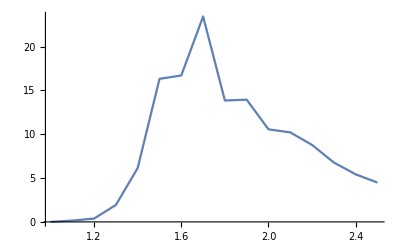

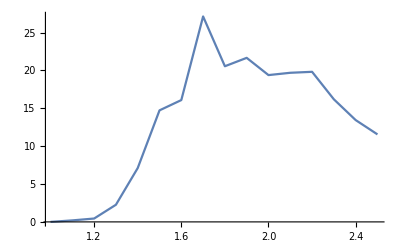

```mathematica
pts=Monitor[
Table[{m,σRes[N938,1/2,pi,-1,m]-σResEl[N938,1/2,pi,-1,m]},{m,1.,2.5,0.1}],
ProgressIndicator[m,{1.,2.5}]];
ListLinePlot[pts,PlotRange->All]
```

```mathematica
σRes[
```

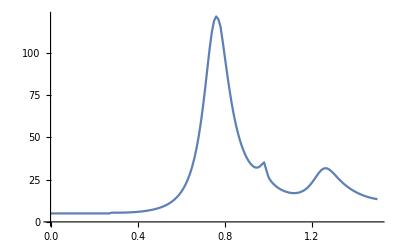

-Graphics-

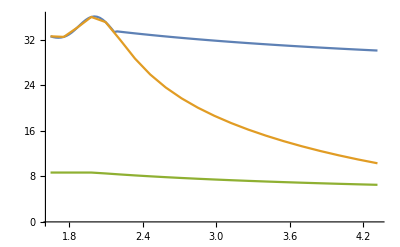

```mathematica
ptsTot=Monitor[
Block[{hA=pi,i3A=+1,hB=pi,i3B=-1},
Table[{
eCM+0pLab[m0@hB,m0@hA,eCM],
5+σRes[hA,i3A,hB,i3B,eCM]},{eCM,0.0,1.5,0.01}]
],{ProgressIndicator[eCM,{0.,1.5}],res}
];
ListLinePlot[ptsTot,PlotRange->{0,All}]
```